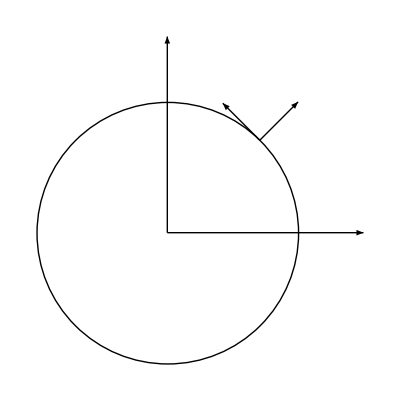

```mathematica
Show[Graphics[Arrow[{{0,0},{0,1.5}}]],Graphics[Arrow[{{0,0},{1.5,0}}]],Graphics[Arrow[{{Cos[π/4],Sin[π/4]},{1,1}}]],Graphics[Circle[]],Graphics[Arrow[{{Cos[π/4],Sin[π/4]},{Cos[π/4]-0.4Sin[π/4],Sin[π/4]+0.4Cos[π/4]}}]]]
```

```mathematica
θ=π/4
ϕ=π/4
```

π/4

π/4

```mathematica
plt=Show[Graphics3D[{Opacity[0.2],Sphere[]}],Graphics3D[{Green,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Green,Arrow[{{0,0,0},{0,2,0}}]}],Graphics3D[{Green,Arrow[{{0,0,0},{0,0,2}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{Sin[θ]Cos[ϕ]-Cos[θ]Cos[ϕ],Sin[θ]Sin[ϕ]-Cos[θ]Sin[ϕ],Cos[θ]+Sin[θ]}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{2Sin[θ]Cos[ϕ],2Sin[θ]Sin[ϕ],2Cos[θ]}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{Sin[θ]Cos[ϕ]-Sin[ϕ],Sin[θ]Sin[ϕ]+Cos[ϕ],Cos[θ]}}]}],Graphics3D[{Blue,Arrow[{{0,0,0},{Cos[ϕ],Sin[ϕ],0}}]}],Graphics3D[{Blue,Arrow[{{0,0,0},{-Sin[ϕ],+Cos[ϕ],0}}]}],
Graphics3D[{Blue,Arrow[{{0,0,0},{Cos[ϕ]-Sin[ϕ],Sin[ϕ]+Cos[ϕ],0}}]}],Graphics3D[Line[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]],Graphics3D[{Yellow,Sphere[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},0.1]}],Graphics3D[Text["(ê)_r",{2Sin[θ]Cos[ϕ]+0.05,2Sin[θ]Sin[ϕ]+0.05,2Cos[θ]+0.05}]],Graphics3D[Text["(ê)_ϕ",{Sin[θ]Cos[ϕ]-Sin[ϕ]-0.05,Sin[θ]Sin[ϕ]+Cos[ϕ]+0.05,Cos[θ]}]],Graphics3D[Text["(ê)_θ",{Sin[θ]Cos[ϕ]-Cos[θ]Cos[ϕ]-0.07,Sin[θ]Sin[ϕ]-Cos[θ]Sin[ϕ]-0.07,Cos[θ]+Sin[θ]-0.05}]],Graphics3D[Text["o⃗",{Cos[ϕ]+0.03,Sin[ϕ]+0.03,-0.05}]],
Graphics3D[Text["u⃗",{Cos[ϕ]-Sin[ϕ]+0.03,Sin[ϕ]+Cos[ϕ],-0.05}]],
Graphics3D[Text["s⃗",{-Sin[ϕ]-0.03,+Cos[ϕ]+0.03,-0.05}]],
Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,2.1,0}]],
Graphics3D[Text["z",{0,0,2.1}]],ViewPoint->{1,0.2,0.5}]
```

-Graphics3D-

```mathematica
SetDirectory["/home/nteixeira/S1_2018_2019/II/Presentation"]
```

/home/nteixeira/Desktop/S1_2018_2019/II/Presentation

```mathematica
Export["Excontrolo4_3.png",Append[plt,Boxed->False],ImageResolution->200]
```

Excontrolo4_3.png

```mathematica
θ=π/6
```

π/6

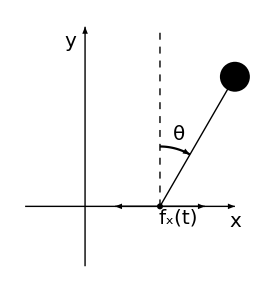

```mathematica
a=Graphics[Line[{{0+0.5,0},{Sin [θ]+0.5,Cos[θ]}}]];
b=Graphics[{Disk[{Sin[θ]+0.5,Cos[θ]},0.1]}];
c=Graphics[Arrow[{{0,-0.4},{0,1.2}}]];
plot1=ParametricPlot[{0.4 Sin[u]+0.5,0.4Cos[u]},{u,0,π/6},Axes->None,ImageSize->Medium,PlotStyle->Black];
d=plot3=plot1/.Line[x_]->{Arrowheads[0.03],Black,Arrow[x]};
e=Graphics[Arrow[{{-0.4,0},{1,0}}]];
f=Graphics[Text[Style["x",FontSize->20],{1,-0.1}]];
g=Graphics[Text[Style["y",FontSize->20],{-0.1,1.1}]];
h=Graphics[Text[Style["θ",FontSize->20],{0.5Sin[θ/2]+0.5,0.5Cos[θ/2]}]];
i=Graphics[Arrow[{{0+0.5,0},{0.3+0.5,0}}]];
j=Graphics[Arrow[{{0+0.5,0},{-0.3+0.5,0}}]];
k=Graphics[{Disk[{0+0.5,0},0.02]}];
l=Graphics[Text[Style["f_x(t)",FontSize->20],{0.12+0.5,-0.08}]];
m=Graphics[{Dashed,Line[{{0.5,0},{0.5,1.2}}]}];
Show[a,b,c,d,e,f,g,h,i,j,k,l,m]
```

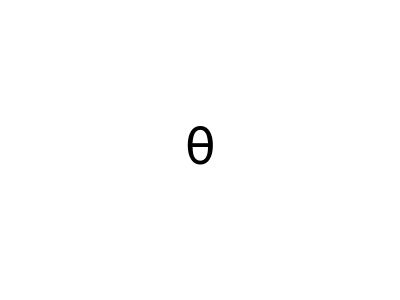

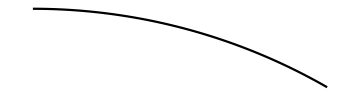

```mathematica
h=Graphics[Text[Style["θ",FontSize->50],{0.5Sin[θ/2],0.5Cos[θ/2]}]]
```

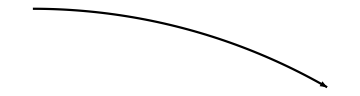

-Graphics-

```mathematica
plot2=plot1/.Line->Arrow
```